## The problem

The examiners want to justify the part of the filter where the track structure is examined.

“After level detection a set of conditions are presented in Section 5.3 with the claim that if satisfied will give high confidence that only two fluorophores are active but this claim does not appear to be verified.(Similar claims are repeated later on and should be tone down unless accompanied by verification.)”

## Proposed Solution

The fluorophore can be in one of 3 states, emission (E), Dark (D), and photobleached (p). It can stay in emission, P(E|E), move from emission to dark, P(D|E), stay in dark, P(D|D), come out of dark state, P(E|D), or move from emission to photobleached, P(P|E). Once a fluorophore is photobleached it cannot move out of that state (P(P|P) = 1).

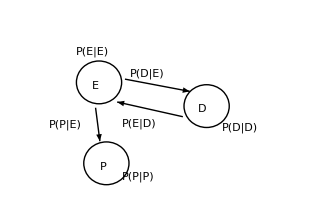

Based on this it can be estimated the probability of different fluorophore configurations given some intensity trace. For example the trace:

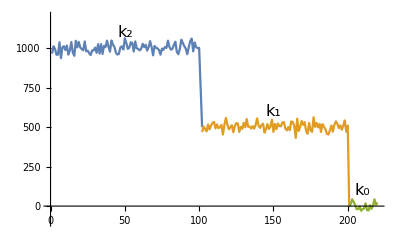

```mathematica
ListLinePlot[
{Transpose[{
Range[1, 102],
Join[RandomInteger[PoissonDistribution[1000], 100],{750}, {500}]
}],
Transpose[{
Range[102, 201],
Join[RandomInteger[PoissonDistribution[500], 99], {0}]
}],
Transpose[{
Range[201, 220],
RandomReal[NormalDistribution[0,20], 20]
}]
},
PlotRange->{{0, 220}, {-100, 1200}},
Epilog->{
Text[Style["k_2",16],{50,1100}],
Text[Style["k_1",16],{150,600}],
Text[Style["k_0",16],{210,100}]
}
]
```

One possible interpretation is that there are two fluorophores in level 2, for k_2 frames, then one of them goes into a dark state or photobleaches then there is only one fluorphore in level 1, for k_1frames, then this fluorophore goes in to a dark state or photobleaches and then there are k_0frames of no fluorescence.

The probability of this happening is ( case 1 ):

P(E|E)^k_2(P(E|D)P(D|D)^(k_1+k_0+1)+P(P|E))P(E|E)^(k_2+k_1+1)(P(E|D)P(D|D)^k_0+ P(P|D))

Another possible interpretation is that there is one active fluorophore in level 2, for k_2frames, then it goes into a dark state or photobleaches, while there is another fluorophore which is in a dark state during this time and come out of a dark states. Then the second fluorophore is in emiting state during level 1, for k_1frames, and it goes into a dark state or photobleaches.

The probability of this happens is ( case 2 ):

P(E|E)^k_2(P(E|D)P(D|D)^(k_1+k_0+1)+P(P|E))P(D|D)^k_2 P(E|D)P(E|E)^k1(P(E|D)P(D|D)^k_0+ P(P|D))

The ratio of these two cases is

(1/(P(E|E)^k_2(P(E|D)P(D|D)^(k_1+k_0+1)+P(P|E))P(D|D)^k_2 P(E|D)P(E|E)^k1(P(E|D)P(D|D)^k_0+ P(P|D))))P(E|E)^k_2(P(E|D)P(D|D)^(k_1+k_0+1)+P(P|E))P(E|E)^(k_2+k_1+1)(P(E|D)P(D|D)^k_0+ P(P|D))

When the terms are canceled out the ratio becomes

(P(E|E)^(k_2+1))/(P(D|D)^k_2 p(E|D))

So which case is more likely depends on the probabilities P(D|D), P(E|D) and P(E|E)

### Evaluating probabilities:

The probabilities P(D|D), P(E|D) and P(E|E) can be evaluated from FLImP tracks. For example take tracks of the type

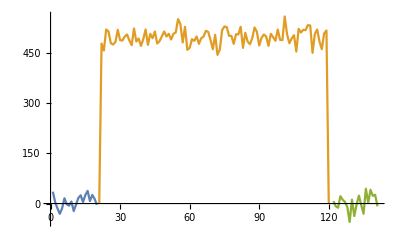

```mathematica
ListLinePlot[
{Transpose[{
Range[1, 20],
RandomReal[NormalDistribution[0,20], 20]
}],
Transpose[{
Range[21, 120],
Join[{0},RandomInteger[PoissonDistribution[500],98], {0}]
}],
Transpose[{
Range[122, 141],
RandomReal[NormalDistribution[0,20], 20]
}]
}
]
```

Can be used to count how many frames the fluorophore has been in emitting state and derive P(E|E)

Then tracks like this:

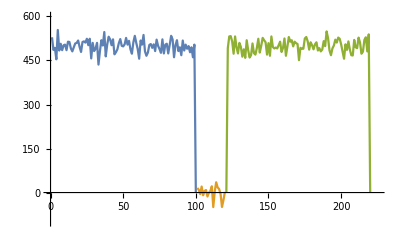

```mathematica
ListLinePlot[
{Transpose[{
Range[1, 100],
Join[RandomInteger[PoissonDistribution[500],99], {0}]
}],
Transpose[{
Range[101, 120],
RandomReal[NormalDistribution[0,20], 20]
}],
Transpose[{
Range[121, 220],
Join[{0},RandomInteger[PoissonDistribution[500],98], {0}]
}]
},
PlotRange->{{0, 225}, {-100, 600}}
]
```

can be used to count how many frames the fluorophore has been in a dark state to derive P(D|D) and P(E|D).

However there is a problem. It is not known what is the probability of a fluorphore to be in a emitting, or a dark state at the beginning of the track.